```mathematica
Clear["Global`*"]
```

```mathematica
(*给定的参数*)m=1;q=1.25;g=1.5;n=1;
(*缩写*)(*定义公式*)f[ω_]:=((3 q^4)/(640n m π))/(√((g n)/m+(2 g^(5/2)m^(1/2)n^(3/2))/π^2))/(2(ω-1)^2+((3 q^4)/(640n m π))^2/((g n)/m+(2 g^(5/2)m^(1/2)n^(3/2))/π^2))

(*画出随 ω 变化的函数图像*)
plot=Plot[f[ω],{ω,0.4,1.3},PlotRange->All,PlotLegends->{"z = 0,rho"},Frame->{{True,True},{True,True}},AxesLabel->{"ω","f(ω)"},PlotStyle->Blue,ImageSize->800,(*Make the entire plot wider*)AspectRatio->0.3];
```

```mathematica
(*给定的参数*)m=1;q=1.25;g=0.5;n=1;g1=1.5;
(*缩写*)(*定义 m**)mStar[z_]:=m/(1+z);
(*缩写*)(*定义公式*)
a[z_]:=((2 g^(5/2)m^(1/2)n^(3/2)z^2)/(π^2(z+1)^(5/2))+(2 g^(5/2)m^(1/2)n^(3/2))/(π^2(1+z)^(1/2))-(4 g^(5/2)m^(1/2)n^(3/2)z)/(π^2(1+z)^(3/2))+(g n(1+z))/m)^(1/2)/((g1 n)/m+(2 g1^(5/2)m^(1/2)n^(3/2))/π^2)^(1/2);
b[z_]:=(g1+(2 g1^(5/2)n^(1/2)m^(3/2))/π^2)/(g+(2 g^(5/2)m^(3/2)n^(1/2)z^2)/(π^2(1+z)^(7/2))-(4 g^(5/2)m^(3/2)n^(1/2)z)/(π^2(1+z)^(5/2))+(2 g^(5/2)m^(3/2)n^(1/2))/(π^2(1+z)^(3/2)));
y[z_,ω_]:=((3 q^4)/(640n mStar[z] π))/(√((g1 n)/m+(2 g1^(5/2)m^(1/2)n^(3/2))/π^2))/(2(ω-a[z])^2+((3 q^4)/(640n mStar[z] π))^2/((g1 n)/m+(2 g1^(5/2)m^(1/2)n^(3/2))/π^2))*a[z]*b[z];

(*画出随 ω 变化的函数图像*)
plot1=Plot[Table[y[z,ω],{z,{0}}],{ω,0.4,1.3},PlotLegends->{"z = 0"},PlotRange->All,AxesLabel->{"ω","f(z, ω)"},Frame->{{True,True},{True,True}},PlotStyle->{Black,Thickness[0.005]},ImageSize->800,(*Make the entire plot wider*)AspectRatio->0.3];
plot2=Plot[Table[y[z,ω],{z,{0.1}}],{ω,0.4,1.3},PlotLegends->{"z = 0.1"},Frame->{{True,True},{True,True}},PlotRange->All,AxesLabel->{"ω","f(z, ω)"},Frame->{{True,True},{True,True}},PlotStyle->{Red,Dashing[{0.004}]},ImageSize->800,(*Make the entire plot wider*)AspectRatio->0.3];
plot3=Plot[Table[y[z,ω],{z,{0.5}}],{ω,0.4,1.3},PlotLegends->{"z = 0.5"},PlotRange->All,AxesLabel->{"ω","f(z, ω)"},Frame->{{True,True},{True,True}},PlotStyle->{Darker[Orange],Dotted},ImageSize->800,(*Make the entire plot wider*)AspectRatio->0.3];
plot4=Plot[Table[y[z,ω],{z,{0.6}}],{ω,0.4,1.3},PlotLegends->{"z = 1"},PlotRange->All,AxesLabel->{"ω","f(z, ω)"},Frame->{{True,True},{True,True}},PlotStyle->{Darker[Green],Dashing[{0.02,0.02}]},ImageSize->800,(*Make the entire plot wider*)AspectRatio->0.3];
```

```mathematica
plot01=Plot[a[z],{z,0,1},PlotRange->All,AxesLabel->{"z","a(z)"},Frame->{{True,True},{True,True}},PlotStyle->{Black,Thickness[0.005]},ImageSize->800,(*Make the entire plot wider*)AspectRatio->0.3];
```

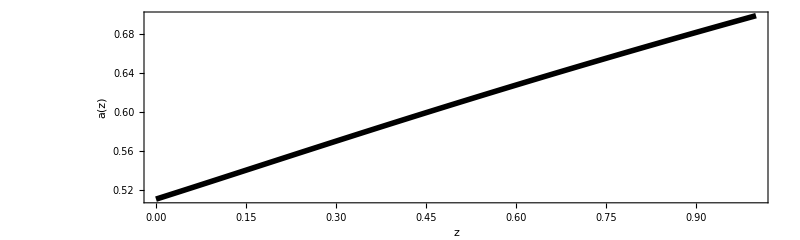

fig3b.eps

```mathematica
Fig4=Show[plot01]
Export["fig3b.eps",Fig4]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fig3b.eps"]]]
```

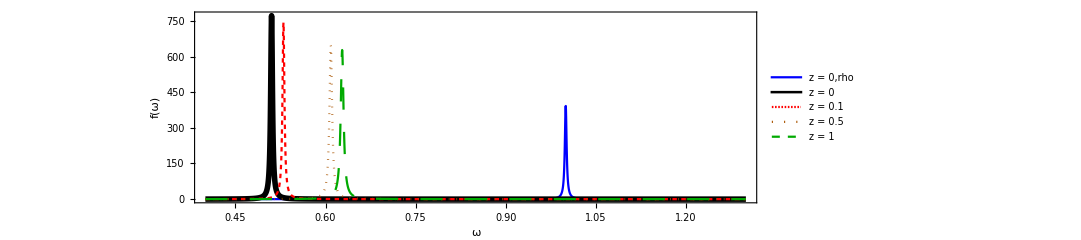

```mathematica
Fig3=Show[plot,plot1,plot2,plot3,plot4]
```

```mathematica
Export["fig3.eps",Fig3]
```

fig3.eps